```mathematica
Select[deps2,Chrom[#[[1]]]>Chrom[#[[2]]]&]
```

{{6,18},{7,18},{20,40},{11,40},{11,36},{14,40},{15,40},{15,36},{18,50},{19,36},{21,38},{41,97},{41,99},{25,114},{25,88},{25,119},{49,142},{49,143},{26,88},{26,160},{26,119},{39,97},{39,113},{39,180},{53,165},{53,160},{53,142},{53,153},{37,142},{37,160},{66,180},2964,{1321,5417},{1000,6893},{1000,4727},{1000,2634},{1000,4739},{1000,4633},{1018,5357},{1018,4689},{1018,4699},{1018,4621},{1018,4631},{1147,6874},{1147,2885},{1147,4877},{1147,6899},{1147,2890},{1147,6888},{1147,4876},{1147,6876},{1147,6885},{1147,6895},{1147,6889},{1256,6859},{1256,4623},{1256,6854},{1256,4632},{1256,7236},{1007,7231},{1007,4861},{1007,7397},{1016,4686}}
 |  |  |  |

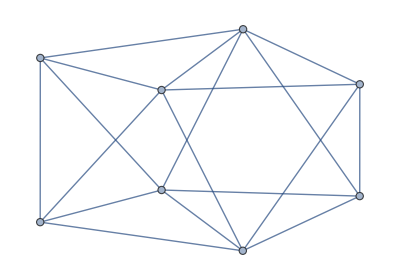

```mathematica
graf18=Graph[{1<->2,1<->3,1<->5,1<->7,1<->8,2<->3,2<->6,2<->7,3<->4,3<->6,3<->8,4<->5,4<->6,4<->8,5<->6,5<->7,5<->8,6<->7}]
```

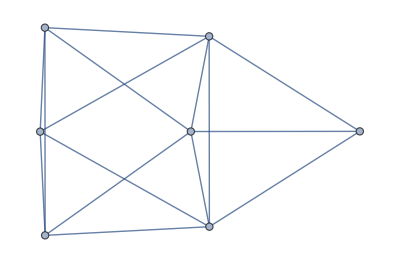

```mathematica
graf6=Graph[{1<->2,1<->3,1<->5,1<->7,2<->3,2<->6,2<->7,3<->4,3<->5,3<->6,4<->5,4<->6,5<->6,5<->7,6<->7}]
```

```mathematica
Length[VertexList[graf6]]
```

7

```mathematica
Chrom[18]/24
```

3

```mathematica
Range[3]
```

{1,2,3}

```mathematica
ChromaticPolynomial[graf6,4]/24
```

4

```mathematica
ChromaticPolynomial[graf18,4]/24
```

3

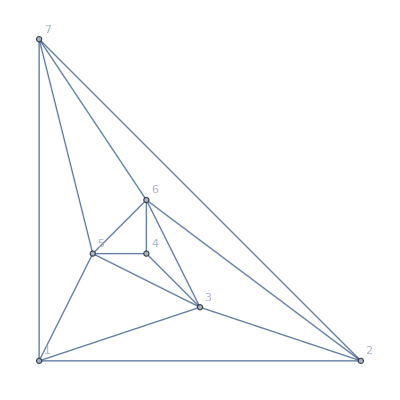

```mathematica
Graph[graf6, VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]
```

```mathematica
ChromaticPolynomial[EdgeDelete[graf18,{8<->4,8<->1}],4]/24
```

14

```mathematica
ChromaticPolynomial[EdgeContract[graf18,{8<->1}],4]/24
```

5

```mathematica
ChromaticPolynomial[EdgeDelete[graf18,{8<->1}],4]/24
```

8

```mathematica
ChromaticPolynomial[EdgeDelete[graf18,{8<->4}],4]/24
```

8

```mathematica
ChromaticPolynomial[EdgeContract[graf18,{8<->4}],4]/24
```

5

```mathematica
ChromaticPolynomial[EdgeAdd[graf6,1<->4],4]/24
```

3

```mathematica
EdgeList[graf18]
```

{1<->2,1<->3,1<->5,1<->7,1<->8,2<->3,2<->6,2<->7,3<->4,3<->6,3<->8,4<->5,4<->6,4<->8,5<->6,5<->7,5<->8,6<->7}

```mathematica
Graph[graf18, VertexLabels->"Name", GraphLayout->"PlanarEmbedding", GraphHighlightStyle->"Dashed", GraphHighlight->{1<->8,3<->8,4<->8,5<->8}]
```

-Graphics-

```mathematica
TableForm[Table[{e,Graph[EdgeContract[graf18,e],ImageSize->100 , GraphLayout->"PlanarEmbedding"],ChromaticPolynomial[EdgeContract[graf18,e],4]/24},{e,Subsets[{1<->8,3<->8,4<->8,5<->8},{2}]}], TableDepth->1]
```

```mathematica
EdgeContract
```

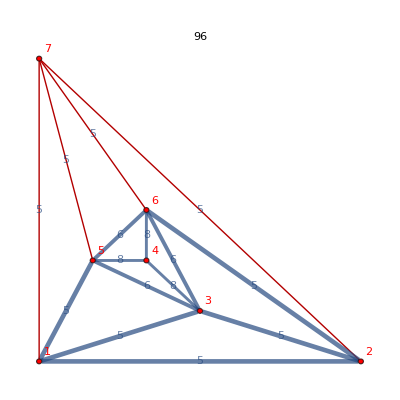

```mathematica
PaintEdgeWeight[graf6]
```

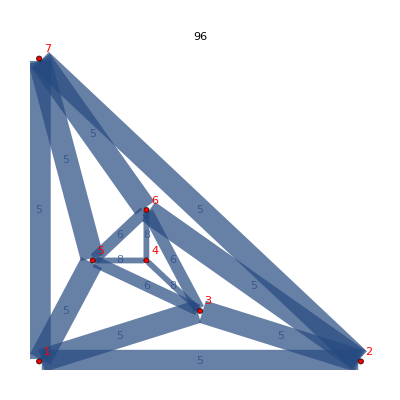

```mathematica
PaintEdgeWeight3[graf6]
```

```mathematica
PaintEdgeWeight3[g_]:=Graph[g,
VertexLabels->"Name",
VertexStyle->Red,
VertexLabelStyle->Red,
EdgeStyle->Table[e->Thickness[1/(ChromaticPolynomial[EdgeContract[g,e],4])],{e,EdgeList[g]}], EdgeLabels->Table[e->ChromaticPolynomial[EdgeDelete[g,e],4]/24,{e,EdgeList[g]}], 
EdgeLabelStyle->Large,
GraphLayout->"PlanarEmbedding",
PlotLabel->ChromaticPolynomial[g,4]/24, 
ImageSize->400]
```

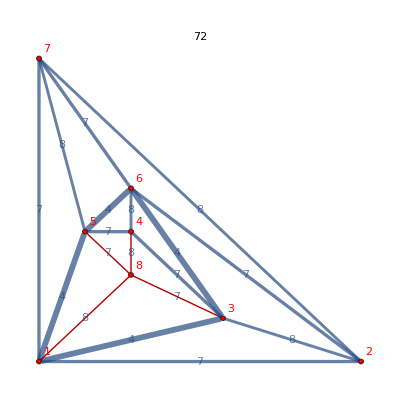

```mathematica
PaintEdgeWeight[graf18]
```

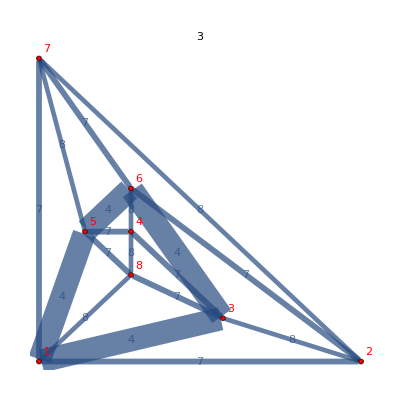

```mathematica
PaintEdgeWeight3[graf18]
```

```mathematica
ChromaticPolynomial[EdgeDelete[graf18,{8<->5}],4]/24
```

7

```mathematica
TableForm[Sort[Table[{ChromaticPolynomial[EdgeContract[graf18,e],4]/24,e,Graph[EdgeContract[graf18,e],ImageSize->100 , GraphLayout->"PlanarEmbedding"]},{e,EdgeList[graf18]}]], TableDepth->1]
```

```mathematica
Needs["Combinatorica`"]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
LayeredGraphPlot[{1<->2,1<->3,1<->5,1<->7,2<->3,2<->6,2<->7,3<->4,3<->5,3<->6,4<->5,4<->6,5<->6,5<->7,6<->7}]
```

LayeredGraphPlot::grph: {1 <-> 2, 1 <-> 3, 1 <-> 5, 1 <-> 7, 2 <-> 3, 2 <-> 6, 2 <-> 7, 3 <-> 4, 3 <-> 5, 3 <-> 6, 4 <-> 5, 4 <-> 6, 5 <-> 6, 5 <-> 7, 6 <-> 7} is not a valid graph.

LayeredGraphPlot[{1<->2,1<->3,1<->5,1<->7,2<->3,2<->6,2<->7,3<->4,3<->5,3<->6,4<->5,4<->6,5<->6,5<->7,6<->7}]

```mathematica
VertexColoring[ReadGrof[6 ]]
```

VertexColoring[-Graphics-]

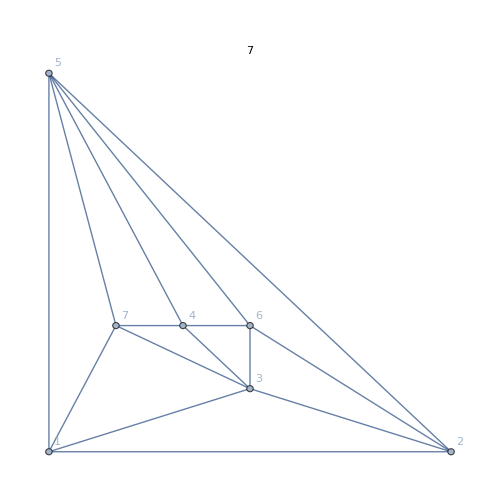
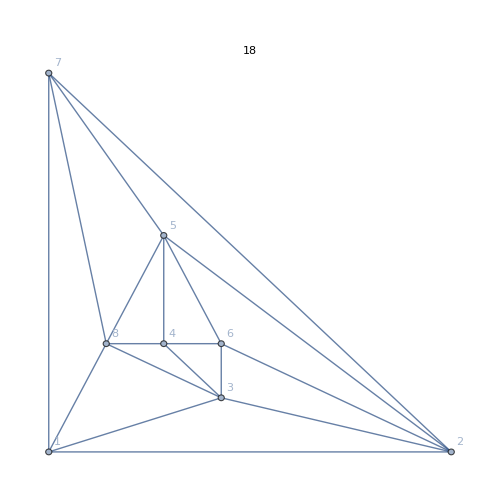
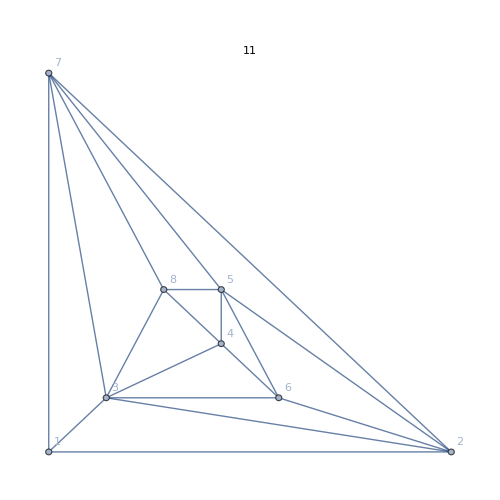
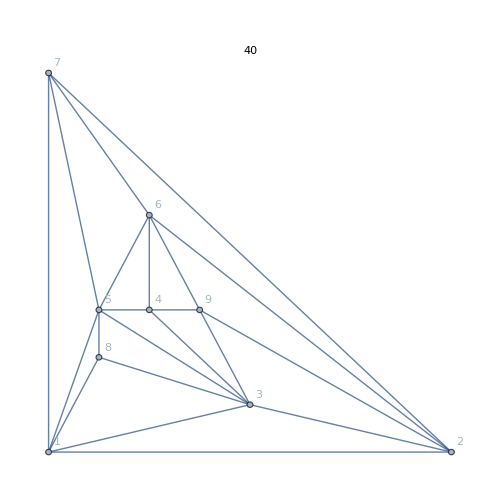
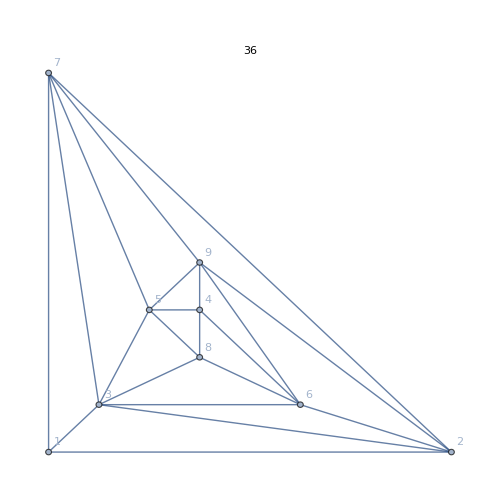
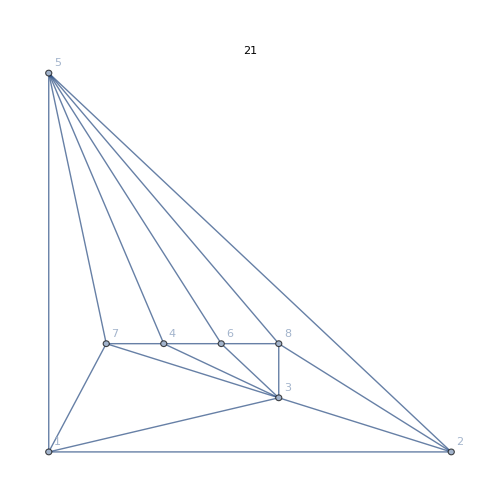
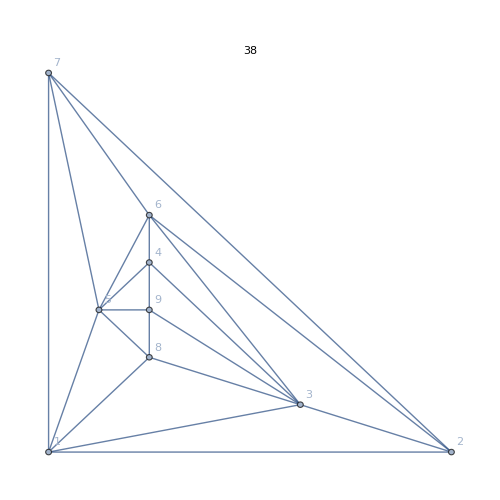
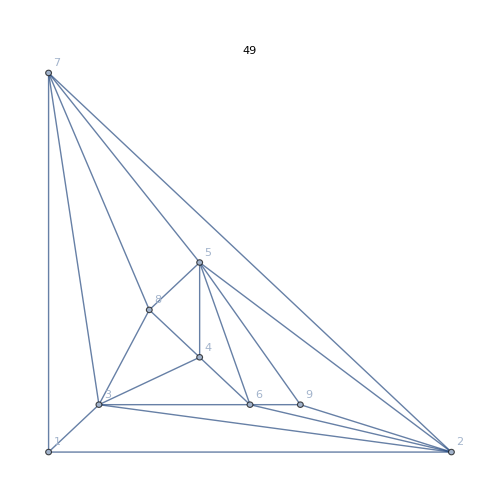
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-

```mathematica
Column[
Table[
Row[{Graph[ReadGrof[k[[1]] ],GraphLayout->"PlanarEmbedding", VertexLabels->"Name", ImageSize->500, PlotLabel->k[[1]]],,Graph[ReadGrof[k[[2]] ],GraphLayout->"PlanarEmbedding", VertexLabels->"Name", ImageSize->500,PlotLabel->k[[2]]]}],
{k,Take[Select[deps2,Chrom[#[[1]]]-24>Chrom[#[[2]]]&],10]}
]
]
```

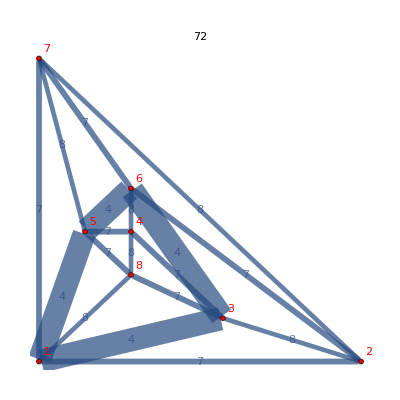

```mathematica
PaintEdgeWeight3[graf18]
```

```mathematica
With[{a=AdjacencyMatrix[graf18]},
{MatrixForm[a ],MatrixForm[a .a],MatrixForm[a .a.a],MatrixForm[a .a.a.a],MatrixForm[a .a.a.a.a],MatrixForm[a .a.a.a.a.a],MatrixForm[a .a.a.a.a.a.a]}]
```

{(0 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 1 | 0 | 0 | 0 | 1
0 | 1 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0 | 1 | 1 | 0),(5 | 2 | 2 | 2 | 2 | 2 | 4 | 3
2 | 4 | 2 | 3 | 2 | 2 | 2 | 2
2 | 2 | 5 | 4 | 3 | 2 | 2 | 2
2 | 3 | 4 | 5 | 2 | 2 | 2 | 2
2 | 2 | 3 | 2 | 4 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2 | 4 | 3 | 2
4 | 2 | 2 | 2 | 2 | 3 | 5 | 2
3 | 2 | 2 | 2 | 2 | 2 | 2 | 4),(10 | 13 | 16 | 16 | 13 | 12 | 11 | 10
13 | 8 | 12 | 10 | 11 | 9 | 13 | 9
16 | 12 | 10 | 11 | 10 | 13 | 16 | 13
16 | 10 | 11 | 10 | 12 | 13 | 16 | 13
13 | 11 | 10 | 12 | 8 | 9 | 13 | 9
12 | 9 | 13 | 13 | 9 | 8 | 10 | 11
11 | 13 | 16 | 16 | 13 | 10 | 10 | 12
10 | 9 | 13 | 13 | 9 | 11 | 12 | 8),(70 | 50 | 56 | 56 | 50 | 52 | 68 | 55
50 | 49 | 52 | 55 | 44 | 44 | 50 | 44
56 | 52 | 70 | 68 | 55 | 50 | 56 | 50
56 | 55 | 68 | 70 | 52 | 50 | 56 | 50
50 | 44 | 55 | 52 | 49 | 44 | 50 | 44
52 | 44 | 50 | 50 | 44 | 49 | 55 | 44
68 | 50 | 56 | 56 | 50 | 55 | 70 | 52
55 | 44 | 50 | 50 | 44 | 44 | 52 | 49),(264 | 244 | 295 | 295 | 244 | 237 | 267 | 232
244 | 196 | 237 | 232 | 204 | 201 | 244 | 201
295 | 237 | 264 | 267 | 232 | 244 | 295 | 244
295 | 232 | 267 | 264 | 237 | 244 | 295 | 244
244 | 204 | 232 | 237 | 196 | 201 | 244 | 201
237 | 201 | 244 | 244 | 201 | 196 | 232 | 204
267 | 244 | 295 | 295 | 244 | 232 | 264 | 237
232 | 201 | 244 | 244 | 201 | 204 | 237 | 196),(1315 | 1070 | 1244 | 1244 | 1070 | 1086 | 1310 | 1094
1070 | 929 | 1086 | 1094 | 916 | 914 | 1070 | 914
1244 | 1086 | 1315 | 1310 | 1094 | 1070 | 1244 | 1070
1244 | 1094 | 1310 | 1315 | 1086 | 1070 | 1244 | 1070
1070 | 916 | 1094 | 1086 | 929 | 914 | 1070 | 914
1086 | 914 | 1070 | 1070 | 914 | 929 | 1094 | 916
1310 | 1070 | 1244 | 1244 | 1070 | 1094 | 1315 | 1086
1094 | 914 | 1070 | 1070 | 914 | 916 | 1086 | 929)}

```mathematica
1,2,13,50,244,1070
```

```mathematica
Det[AdjacencyMatrix[graf18]]
```

21

```mathematica
Det[AdjacencyMatrix[graf6]]
```

0

```mathematica
ChromaticPolynomial[graf6,x]
```

192 x-526 x^2+565 x^3-311 x^4+94 x^5-15 x^6+x^7

```mathematica
Factor[ChromaticPolynomial[graf6,x]]
```

(-3+x) (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3)

```mathematica
Factor[ChromaticPolynomial[graf18,x]]
```

(-3+x) (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4)

```mathematica
VertexColors[]
```

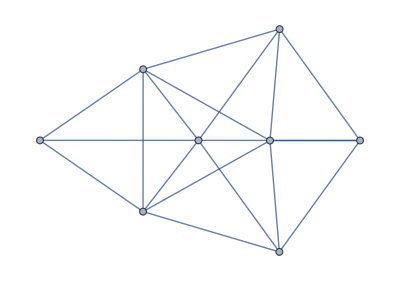

```mathematica
graph11=Graph[{1<->2,1<->3,1<->7,2<->3,2<->5,2<->6,2<->7,3<->4,3<->6,3<->7,3<->8,4<->5,4<->6,4<->8,5<->6,5<->7,5<->8,7<->8}]
```

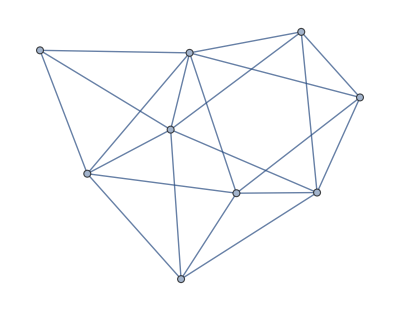

```mathematica
graph40=Graph[{1<->2,1<->3,1<->7,2<->3,2<->5,2<->6,2<->7,2<->9,3<->4,3<->7,3<->8,3<->9,4<->5,4<->6,4<->8,4<->9,5<->6,5<->7,5<->8,6<->9,7<->8}]
```

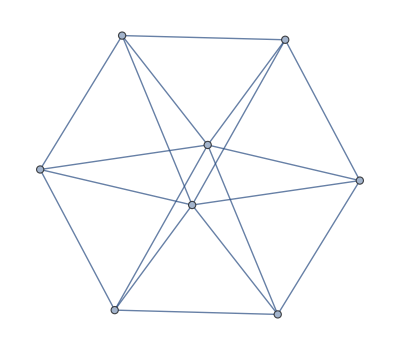

```mathematica
graph21=Graph[{1<->2,1<->3,1<->5,1<->7,2<->3,2<->5,2<->8,3<->4,3<->6,3<->7,3<->8,4<->5,4<->6,4<->7,5<->6,5<->7,5<->8,6<->8}]
```

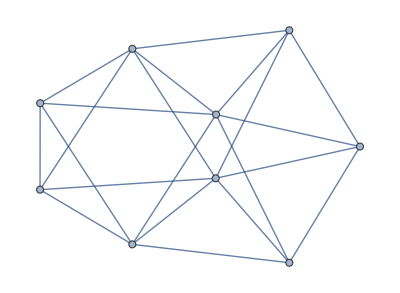

```mathematica
graph38=Graph[{1<->2,1<->3,1<->7,1<->9,2<->3,2<->5,2<->8,2<->9,3<->4,3<->6,3<->7,3<->8,4<->5,4<->6,4<->7,5<->6,5<->7,5<->8,5<->9,6<->8,7<->9}]
```

```mathematica
AcyclicGraphQ[graph40]
```

False

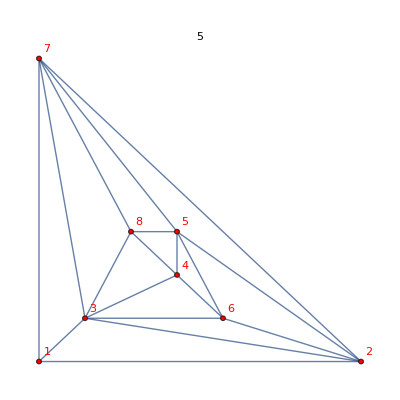
-Graphics--Graphics-

```mathematica
Row[{Graph[graph11, VertexLabels->"Name",
VertexStyle->Red,
VertexLabelStyle->Red,
GraphLayout->"PlanarEmbedding",
PlotLabel->ChromaticPolynomial[graph11,4]/24, 
ImageSize->400],
Graph[graph40, VertexLabels->"Name",
VertexStyle->Red,
VertexLabelStyle->Red,
GraphLayout->"PlanarEmbedding",
PlotLabel->ChromaticPolynomial[graph40,4]/24, 
ImageSize->400, 
GraphHighlight->Select[EdgeList[graph40],#[[1]]==9||#[[2]]==9&],
GraphHighlightStyle->"Dashed"]}]
```

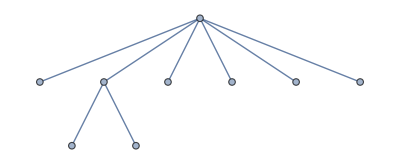

```mathematica
FindSpanningTree[{graph40,2}]
```

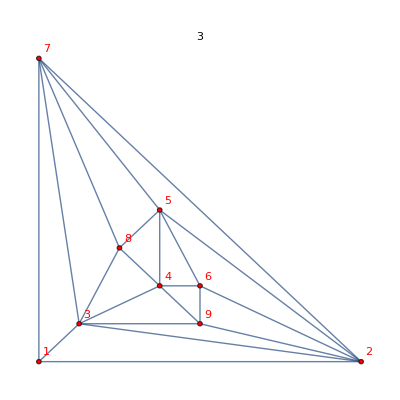

```mathematica
Graph[graph40, VertexLabels->"Name",
VertexStyle->Red,
VertexLabelStyle->Red,
GraphLayout->"PlanarEmbedding",
PlotLabel->ChromaticPolynomial[graph40,4]/24, 
ImageSize->400]
```

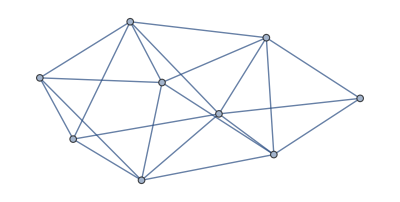

```mathematica
graph36=Graph[{1<->2,1<->3,1<->7,2<->3,2<->5,2<->6,2<->7,3<->6,3<->7,3<->8,3<->9,4<->5,4<->6,4<->8,4<->9,5<->6,5<->7,5<->8,6<->9,7<->8,8<->9}]
```

```mathematica
Row[{Graph[graph11, VertexLabels->"Name",
VertexStyle->Red,
VertexLabelStyle->Red,
GraphLayout->"PlanarEmbedding",
PlotLabel->ChromaticPolynomial[graph11,4]/24, 
ImageSize->400],
Graph[graph36, VertexLabels->"Name",
VertexStyle->Red,
VertexLabelStyle->Red,
GraphLayout->"PlanarEmbedding",
PlotLabel->ToString[ChromaticPolynomial[graph36,4]/24 ]<> "over 3<>4", 
ImageSize->400, 
GraphHighlight->Select[EdgeList[graph36],#[[1]]==9||#[[2]]==9&],
GraphHighlightStyle->"Dashed"]}]
```

-Graphics--Graphics-

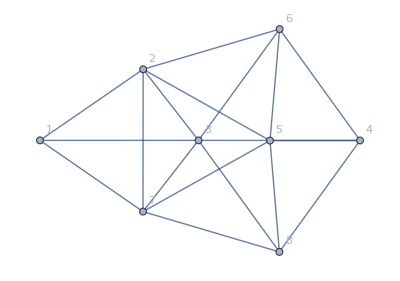

```mathematica
Graph[graph11,VertexLabels->"Name", GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
GraphEmbedding[graph11,"SpringElectricalEmbedding"]
```

{{0.,0.84898},{0.785029,1.39006},{1.20628,0.848905},{0.784181,0.306574},{1.75024,0.847428},{1.82356,1.69592},{2.4354,0.848021},{1.82174,0.}}

```mathematica
({1.2062785975555441,0.8489053156058426}+{0.7841813693041638,0.30657352481741384})/2
```

{0.99523,0.577739}

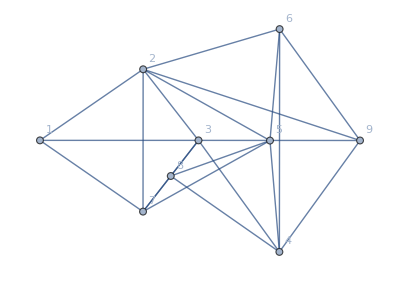

```mathematica
Graph[graph40,VertexLabels->"Name", VertexCoordinates->{{0.,0.8489799943606098},{0.7850290729372387,1.3900606910101068},{1.2062785975555441,0.8489053156058426},{0.7841813693041638,0.30657352481741384},{1.750239355425028,0.8474276774628842},{1.823564328977572,1.6959241461590127},{2.4354017890984982,0.8480207430712144},{1.821737510610574,0.},{0.9952299834298539,0.5777394202116282}}]
```

```mathematica
GraphEmbedding[Graph[graph40,VertexLabels->"Name", VertexCoordinates->{{0.,0.8489799943606098},{0.7850290729372387,1.3900606910101068},{1.2062785975555441,0.8489053156058426},{0.7841813693041638,0.30657352481741384},{1.750239355425028,0.8474276774628842},{1.823564328977572,1.6959241461590127},{2.4354017890984982,0.8480207430712144},{1.821737510610574,0.},{0.9952299834298539,0.5777394202116282}}]]
```

{{0.,0.84898},{0.785029,1.39006},{1.20628,0.848905},{0.784181,0.306574},{1.75024,0.847428},{1.82356,1.69592},{2.4354,0.848021},{1.82174,0.},{0.99523,0.577739}}

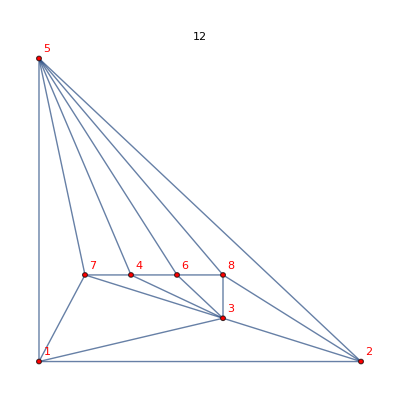
-Graphics--Graphics-

```mathematica
Row[{Graph[graph21, VertexLabels->"Name",
VertexStyle->Red,
VertexLabelStyle->Red,
GraphLayout->"PlanarEmbedding",
PlotLabel->ChromaticPolynomial[graph21,4]/24, 
ImageSize->400],
Graph[graph38, VertexLabels->"Name",
VertexStyle->Red,
VertexLabelStyle->Red,
GraphLayout->"PlanarEmbedding",
PlotLabel->ToString[ChromaticPolynomial[graph38,4]/24 ]<> " over 1<>5", 
ImageSize->400, 
GraphHighlight->Select[EdgeList[graph38],#[[1]]==9||#[[2]]==9&],
GraphHighlightStyle->"Dashed"]}]
```